```mathematica
Resolve[ForAll[{a,b},Element[{a,b},Integers]&&OddQ[a]&&OddQ[b],EvenQ[a+b]]]
```

True

```mathematica
Prove[ForAll[{a,b},Element[{a,b},PositiveReals],a^2+b^2==c^2],{"Assuming"->"c > 0"},"Method"->"EquationalLogic"]
```

Prove[∀_({a,b},(a|b)∈ℝ&&a>0&&b>0)a^2+b^2==c^2,{Assuming→c > 0},Method→EquationalLogic]

```mathematica
Prove[ForAll[{x,y,z},Element[{x,y,z},Reals]&&x+y+z==0,x^3+y^3+z^3==3 x y z]]
```

Prove[∀_({x,y,z},(x|y|z)∈ℝ&&x+y+z==0)x^3+y^3+z^3==3 x y z]

```mathematica
FullSimplify[Prove[∀_({x,y,z},(x|y|z)∈Reals&&x+y+z==0)x^3+y^3+z^3==3 x y z]]
```

Prove[True]

```mathematica
f[x]+f[1-x]/.f->g
```

g[1-x]+g[x]

```mathematica
p1=p2;p1[x,y]
```

p2[x,y]

```mathematica
pf[f_,x_]:=f[x]+f[1-x]
```

```mathematica
pf[Log,q]
```

Log[1-q]+Log[q]

```mathematica
InverseFunction[ArcSin]
```

Sin

```mathematica
%[x]
```

Sin[x]

```mathematica
InverseFunction[f][x]
```

f^(-1)[x]

```mathematica
Nest[f,x,4]
```

f[f[f[f[x]]]]

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

```mathematica
recip[x_]:=1/(1+x)
```

```mathematica
Nest[recip,x,3]
```

1/(1+1/(1+1/(1+x)))

```mathematica
NestList[recip,x,3]
```

{x,1/(1+x),1/(1+1/(1+x)),1/(1+1/(1+1/(1+x)))}

```mathematica
newton3[x_]:=N[1/2(x+3/x)]
```

```mathematica
NestList[newton3,1.0,5]
```

{1.,2.,1.75,1.73214,1.73205,1.73205}

```mathematica
FixedPoint[newton3,1.0]
```

1.73205

```mathematica
FixedPointList[newton3,1.0]
```

{1.,2.,1.75,1.73214,1.73205,1.73205,1.73205}

```mathematica
divide2[n_]:=n/2
```

```mathematica
NestWhileList[divide2,123456,EvenQ]
```

{123456,61728,30864,15432,7716,3858,1929}

```mathematica
NestWhileList[newton3,1.0,Unequal,2]
```

{1.,2.,1.75,1.73214,1.73205,1.73205,1.73205}

```mathematica
NestWhileList[Mod[5#,7]&,1,Unequal,All]
```

{1,5,4,6,2,3,1}

```mathematica
FoldList[f,x,{a,b,c}]
```

{x,f[x,a],f[f[x,a],b],f[f[f[x,a],b],c]}

```mathematica
Fold[f,x,{a,b,c}]
```

f[f[f[x,a],b],c]

```mathematica
FoldList[Plus,0,{a,b,c}]
```

{0,a,a+b,a+b+c}

```mathematica
nextDigit[a_,b_]:=10a+b
```

```mathematica
fromDigits[digits_]:=Fold[nextDigit,0,digits]
```

```mathematica
fromDigits[{1,3,7,2,9,1}]
```

137291

```mathematica
Apply[f,{a,b,c}]
```

f[a,b,c]

```mathematica
Apply[Times,{a,b,c}]
```

a b c

```mathematica
geom[list_]:=Apply[Times,list]^(1/Length[list])
```

```mathematica
geom[{1,2,3,4}]
```

2^(3/4) 3^(1/4)

```mathematica
m={{a,b,c},{b,c,d}}//MatrixForm
```

(a | b | c
b | c | d)

```mathematica
Apply[f,m]
```

f[{{a,b,c},{b,c,d}}]

```mathematica
Apply[f,m,{1}]
```

f[{a,b,c},{b,c,d}]

```mathematica
Apply[f,m,{0,1}]
```

f[f[{a,b,c},{b,c,d}]]

```mathematica
take2[list_]:=Take[list,2]
```

```mathematica
Map[take2,{{1,3,4},{5,6,7},{2,1,6,6}}]
```

{{1,3},{5,6},{2,1}}

```mathematica
Map[f,a+b+c]
```

f[a]+f[b]+f[c]

```mathematica
a+b+c//FullForm
```

Plus[a,b,c]

```mathematica
Map[Sqrt,g[x^2,x^3]]
```

g[√(x^2),√(x^3)]

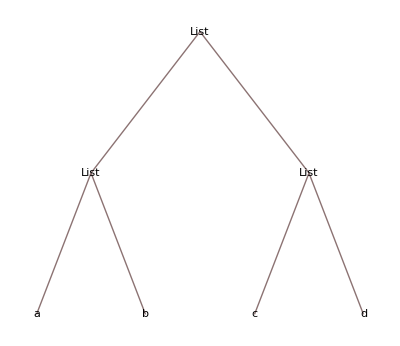

```mathematica
(m={{a,b},{c,d}})//TreeForm
```

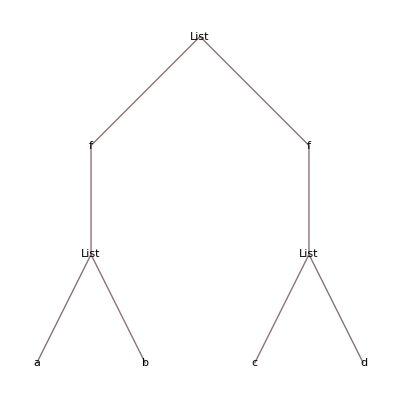

```mathematica
Map[f,m]//TreeForm
```

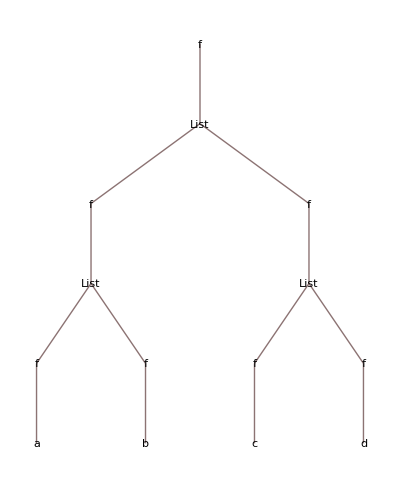

```mathematica
Map[f,m,All]//TreeForm
```

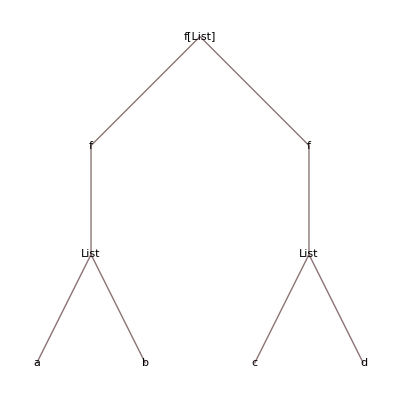

```mathematica
Map[f,m,Heads->True]//TreeForm
```

```mathematica
t=1+(3+x)^2/x
```

1+(3+x)^2/x

```mathematica
FullForm[t]
```

Plus[1,Times[Power[x,-1],Power[Plus[3,x],2]]]

```mathematica
MapAt[f,t,{{2,1,1},{2,2}}]
```

1+f[(3+x)^2]/f[x]

```mathematica
MapIndexed[f,{a,b,c}]
```

{f[a,{1}],f[b,{2}],f[c,{3}]}

```mathematica
MapThread[f,{{a,b,c},{ap,bp,cp}}]
```

{f[a,ap],f[b,bp],f[c,cp]}

```mathematica
Scan[Print,{a,b,c}]
```

a

b

c

```mathematica
Map[Print,{a,b,c}]
```

a

b

c

{Null,Null,Null}

```mathematica
Scan[Print,1+x^2,Infinity]
```

1

x

2

x^2

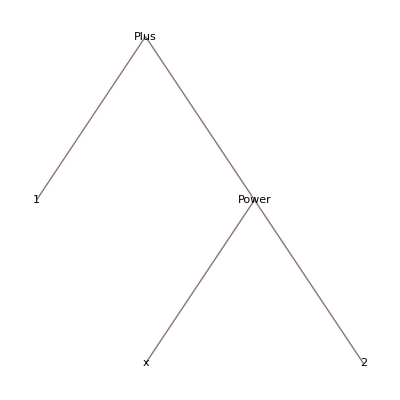

```mathematica
1+x^2//TreeForm
```

```mathematica
h[x_]:=f[x]+g[x]
```

```mathematica
Map[h,{a,b,c}]
```

{f[a]+g[a],f[b]+g[b],f[c]+g[c]}

```mathematica
Map[f[#]+g[#]&,{a,b,c}]
```

{f[a]+g[a],f[b]+g[b],f[c]+g[c]}

```mathematica
f[##,##]&[x,y]
```

f[x,y,x,y]

```mathematica
Apply[f[##2,#1]&,{{a,b,c},{ap,bp}},{1}]
```

{f[b,c,a],f[bp,ap]}

```mathematica
Apply[f[##2,#1]&,{{a,b,c},{ap,bp}}]
```

f[{ap,bp},{a,b,c}]

```mathematica
f[##2,#1]&@@@{{a,b,c},{ap,bp}}
```

{f[b,c,a],f[bp,ap]}

```mathematica
Array[f,n]
```

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[f,n].

Array[f,n]

```mathematica
Array[f,10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
Array[f,{1,2,3}]//MatrixForm
```

((f[1,1,1]
f[1,1,2]
f[1,1,3]) | (f[1,2,1]
f[1,2,2]
f[1,2,3]))

```mathematica
Table[p[i],{i,5}]
```

{p[1],p[2],p[3],p[4],p[5]}

```mathematica
Array[#+#^2&,5]
```

{2,6,12,20,30}

```mathematica
Array[Plus[##]^2&,{3，3}]
```

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[(+##1)^2&,{9 ，}].

Array[(+##1)^2&,{9 ，}]

```mathematica
NestList[D[#,x]&,x^n,3]
```

{x^n,n x^(-1+n),(-1+n) n x^(-2+n),(-2+n) (-1+n) n x^(-3+n)}

```mathematica
Select[{2,15,1,a,16,17},#>4&]
```

{15,16,17}

```mathematica
t=Expand[(x+y+z)^2]
```

x^2+2 x y+y^2+2 x z+2 y z+z^2

```mathematica
Select[t,FreeQ[#,x]&]
```

y^2+2 y z+z^2

```mathematica
f[3][x,y]
```

f[3][x,y]

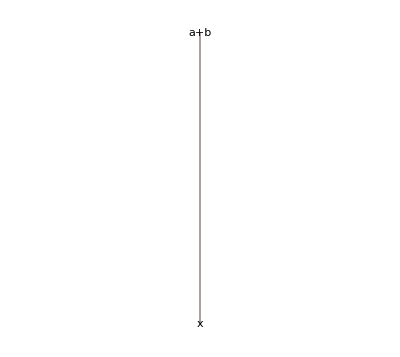

```mathematica
(a+b)[x]//TreeForm
```

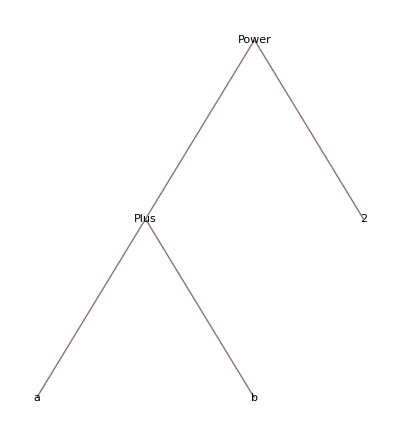

```mathematica
Function[x,x^2][a+b]//TreeForm
```

```mathematica
NDSolve[{y''[x]==y[x],y[0]==y'[0]==1},y,{x,0,5}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
First[%]
```

{y→InterpolatingFunction[…]}

```mathematica
y/.%
```

InterpolatingFunction[…]

```mathematica
%[3.8]
```

44.7012

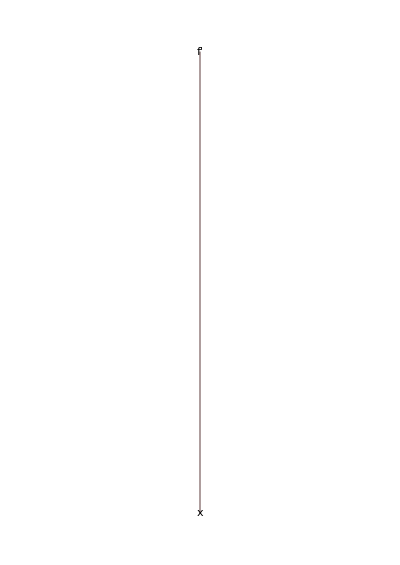

```mathematica
f'[x]//TreeForm
```

```mathematica
f'[x]//Head
```

f'

```mathematica
Composition[f,g,h]
```

f@*g@*h

```mathematica
InverseFunction[Composition[%,q]]
```

q^(-1)@*h^(-1)@*g^(-1)@*f^(-1)

```mathematica
(f+g)[x]
```

(f+g)[x]

```mathematica
Through[%,Plus]
```

f[x]+g[x]

```mathematica
Identity+(D[#,x]&)
```

Identity+(∂_x #1&)

```mathematica
%[x^2]
```

(Identity+(∂_x #1&))[x^2]

```mathematica
Through[%,Plus]
```

2 x+x^2

```mathematica
t=((1+a)(1+b))[x]
```

((1+a) (1+b))[x]

```mathematica
Expand[%]
```

((1+a) (1+b))[x]

```mathematica
MapAll[Expand,t,Heads->True]
```

(1+a+b+a b)[x]

```mathematica
t/.a->1
```

(2 (1+b))[x]

```mathematica
Operator[p,t]
```

Operator[p,((1+a) (1+b))[x]]

```mathematica
Sort[f[c,a,b]]
```

f[a,b,c]

```mathematica
Sort[{5,1,8,2},(#1>#2)&]
```

{8,5,2,1}

```mathematica
Sort[{x^2,y,x+y,y-2},FreeQ[#1,x]&]
```

{y,-2+y,x+y,x^2}

```mathematica
Flatten[f[a,f[b,c],f[f[d]]]]
```

f[a,b,c,d]

```mathematica
Flatten[{a,f[b,c],f[a,b,d]},1,f]
```

{a,b,c,a,b,d}

```mathematica
Distribute[f[a+b]]
```

f[a]+f[b]

```mathematica
Distribute[f[a+b,c+d]]
```

f[a,c]+f[a,d]+f[b,c]+f[b,d]

```mathematica
Log[{a,b,c}]
```

{Log[a],Log[b],Log[c]}

```mathematica
Outer[f,{a,b},{1,2,3}]
```

{{f[a,1],f[a,2],f[a,3]},{f[b,1],f[b,2],f[b,3]}}

```mathematica
Outer[Greater,{1,2,3},{1,2,3}]
```

{{False,False,False},{True,False,False},{True,True,False}}

```mathematica
Outer[g,f[a,b],f[c,d]]
```

f[f[g[a,c],g[a,d]],f[g[b,c],g[b,d]]]

```mathematica
Inner[f,{a,b},{c,d},g]
```

g[f[a,c],f[b,d]]

```mathematica
Inner[Times,{a,b},{c,d},Plus]
```

a c+b d

```mathematica
Flatten[{a,{b,c},{d,e}}]
```

{a,b,c,d,e}

```mathematica
FlattenAt[{a,{b,c},{d,e}},2]
```

{a,b,c,{d,e}}

```mathematica
{a,Sequence[b,c],Sequence[d,e]}
```

{a,b,c,d,e}

```mathematica
{a,b,f[x,y],g[w],f[z,y]}/.f->Sequence
```

{a,b,x,y,g[w],z,y}